```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<IsingScalingFunction`
```

InverseCoordinates::shdw: Symbol InverseCoordinates appears in multiple contexts {IsingScalingFunction`,Global`}; definitions in context IsingScalingFunction` may shadow or be shadowed by other definitions.

```mathematica
N[{γ,10^-4,1-10^-4,10^-4},30]
```

{γ,0.0001,0.9999,0.0001}

```mathematica
data=Table[{ut[1,γ Data[n]["θ0"]](uh[Data[n]["θ0"],Data[n]["gs"]][1,γ Data[n]["θ0"]])^(-8/15),Re@(DScriptF0DηList@@PrepareArgument[Data[n]])[0,γ Data[n]["θ0"]][[1]]},{n,2,6},Evaluate@N[{γ,10^-4,1-10^-4,10^-4},30]];
```

```mathematica
dataf=Interpolation/@data;
```

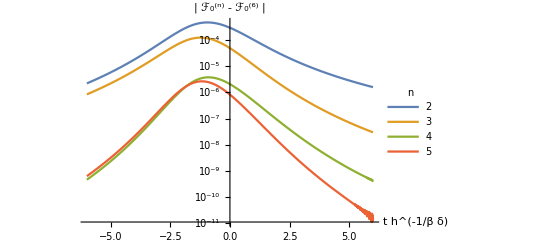

```mathematica
pCovergence=LogPlot[Evaluate[(Abs[#[x]-Last[dataf][x]])&/@Most[dataf]],{x,-6,6},PlotLegends->LineLegend[{2,3,4,5},LegendLabel->"n"],AxesLabel->{"t h^(-1/β δ)","| ℱ_0^(n) - ℱ_0^(6) |"},LabelStyle->{Black,FontSize->12}]
```

```mathematica
Export["/tmp/pConvergence.pdf",pCovergence];
```

```mathematica
data1=Table[{ut[1,γ Data[n]["θ0"]](uh[Data[n]["θ0"],Data[n]["gs"]][1,γ Data[n]["θ0"]])^(-8/15),Re@(DScriptF0DηList@@PrepareArgument[Data[n]])[1,γ Data[n]["θ0"]][[-1]]},{n,2,6},Evaluate@N[{γ,10^-4,1-10^-4,10^-4},30]];
```

```mathematica
data1f=Interpolation/@data1;
```

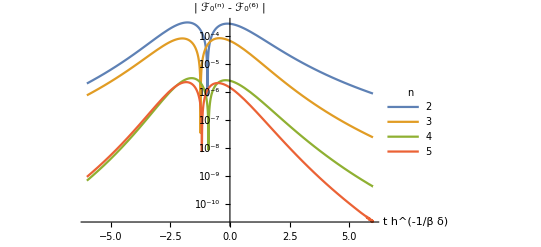

```mathematica
LogPlot[Evaluate[(Abs[#[x]-Last[data1f][x]])&/@Most[data1f]],{x,-6,6},PlotLegends->LineLegend[{2,3,4,5},LegendLabel->"n"],AxesLabel->{"t h^(-1/β δ)","| ℱ_0^(n) - ℱ_0^(6) |"},LabelStyle->{Black,FontSize->12}]
```

```mathematica
ParametricPlot[Evaluate@{
{ut[1,γ Data[2]["θ0"]](uh[Data[2]["θ0"],Data[2]["gs"]][1,γ Data[2]["θ0"]])^(-8/15),(DScriptF0DηList@@PrepareArgument[Data[2]])[0,γ Data[2]["θ0"]]},
{ut[1,γ Data[6]["θ0"]](uh[Data[6]["θ0"],Data[6]["gs"]][1,γ Data[6]["θ0"]])^(-8/15),(DScriptF0DηList@@PrepareArgument[Data[6]])[0,γ Data[6]["θ0"]]}
},{γ,0,0.999},
AspectRatio->1
]
```

```mathematica
1 * 3*2
```

6

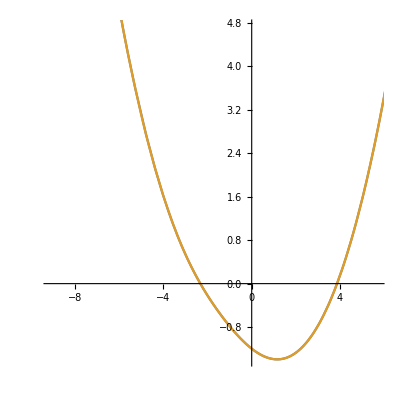

```mathematica
ParametricPlot[Evaluate@{
{ut[1,γ Data[2]["θ0"]](uh[Data[2]["θ0"],Data[2]["gs"]][1,γ Data[2]["θ0"]])^(-8/15),(DScriptF0DηList@@PrepareArgument[Data[2]])[0,γ Data[2]["θ0"]]},
{ut[1,γ Data[6]["θ0"]](uh[Data[6]["θ0"],Data[6]["gs"]][1,γ Data[6]["θ0"]])^(-8/15),(DScriptF0DηList@@PrepareArgument[Data[6]])[0,γ Data[6]["θ0"]]}
},{γ,0,0.999},
AspectRatio->1
]
```

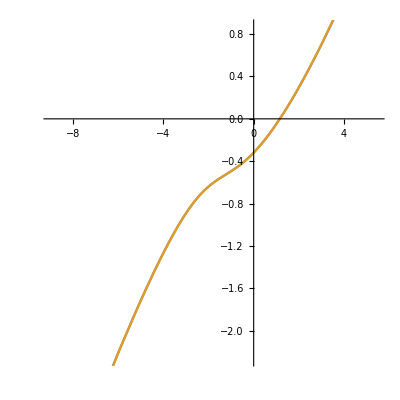

```mathematica
p2=ParametricPlot[Evaluate@{
{ut[1,γ Data[2]["θ0"]](uh[Data[2]["θ0"],Data[2]["gs"]][1,γ Data[2]["θ0"]])^(-8/15),Last@(DScriptF0DηList@@PrepareArgument[Data[2]])[1,γ Data[2]["θ0"]]},
{ut[1,γ Data[6]["θ0"]](uh[Data[6]["θ0"],Data[6]["gs"]][1,γ Data[6]["θ0"]])^(-8/15),Last@(DScriptF0DηList@@PrepareArgument[Data[6]])[1,γ Data[6]["θ0"]]}
},{γ,0,0.999},
AspectRatio->1
]
```

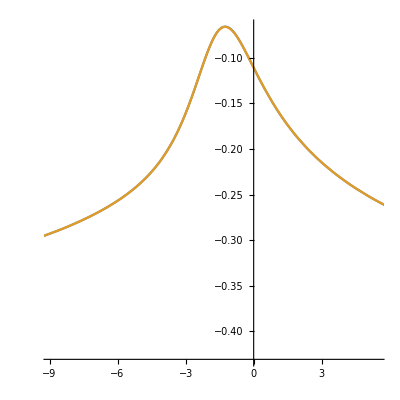

```mathematica
p2=ParametricPlot[Evaluate@{
{ut[1,γ Data[2]["θ0"]](uh[Data[2]["θ0"],Data[2]["gs"]][1,γ Data[2]["θ0"]])^(-8/15),-Last@(DScriptF0DηList@@PrepareArgument[Data[2]])[2,γ Data[2]["θ0"]]},
{ut[1,γ Data[6]["θ0"]](uh[Data[6]["θ0"],Data[6]["gs"]][1,γ Data[6]["θ0"]])^(-8/15),-Last@(DScriptF0DηList@@PrepareArgument[Data[6]])[2,γ Data[6]["θ0"]]}
},{γ,0,0.999},
AspectRatio->1
]
```

```mathematica
uh[Data[2]["θ0"],Data[2]["gs"]][1,γ Data[2]["θ0"]] Abs[ut[1,γ Data[2]["θ0"]]]^(-15/8)
```

((1-γ^2) ((3409755417054688 γ)/7945377693816643-(53028535852605246071985852489792 γ^3)/1618221648977661669617116917623881))/(Abs[-1+(47278060980595344 γ^2)/35848204582560841]^(15/8))

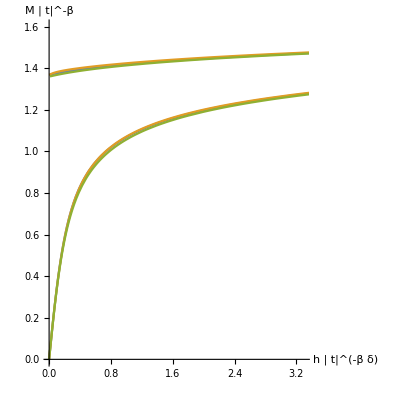

```mathematica
pMag=Show[ParametricPlot[Evaluate@{
{ξ[Data[2]["θ0"],Data[2]["gs"]][γ Data[2]["θ0"]],-(DufDuh@@PrepareArgument[Data[2]])[1][1,γ Data[2]["θ0"]] Abs[ut[1,γ Data[2]["θ0"]]]^(-1/8)},
{ξ[Data[6]["θ0"],Data[6]["gs"]][γ Data[6]["θ0"]],-(DufDuh@@PrepareArgument[Data[6]])[1][1,γ Data[6]["θ0"]] Abs[ut[1,γ Data[6]["θ0"]]]^(-1/8)},
{ξ[θ0Cas,gsCas][γ θ0Cas],DScriptMCasDξList[1,γ θ0Cas][[1]]}
},{γ,0,0.999},PlotRange->{{0,3.3},{0,1.6}},
AspectRatio->1,PlotPoints->50,AxesLabel->{"h | t|^(-β δ)","M | t|^-β"},LabelStyle->{Black,FontSize->14}
]]
```

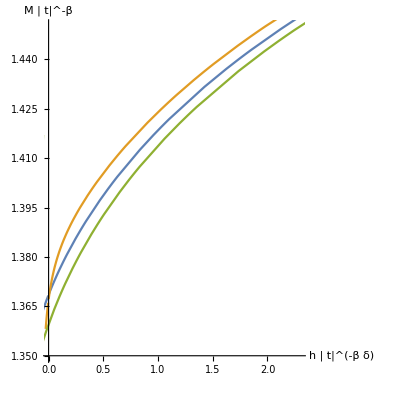

```mathematica
pMag=Show[ParametricPlot[Evaluate@{
{ξ[Data[2]["θ0"],Data[2]["gs"]][θ],-(DufDuh@@PrepareArgument[Data[2]])[1][1,θ] Abs[ut[1,θ]]^(-1/8)},
{ξ[Data[6]["θ0"],Data[6]["gs"]][θ],-(DufDuh@@PrepareArgument[Data[6]])[1][1,θ] Abs[ut[1,θ]]^(-1/8)},
{ξ[θ0Cas,gsCas][θ],DScriptMCasDξList[1,θ][[1]]}
},{θ,0,1.4},
AspectRatio->1,PlotPoints->50,AxesLabel->{"h | t|^(-β δ)","M | t|^-β"},LabelStyle->{Black,FontSize->14},PlotRange->{{0,2.3},{1.35,1.45}}
]]
```

```mathematica
Gls[[2]]//N
```

-1.35784

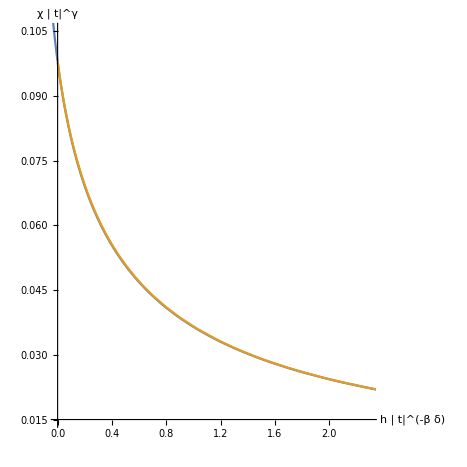

```mathematica
pSus=Show[ParametricPlot[Evaluate@{
{uh[Data[2]["θ0"],Data[2]["gs"]][1,θ] Abs[ut[1,θ]]^(-15/8),-(DufDuh@@PrepareArgument[Data[2]])[2][1,θ] Abs[ut[1,θ]]^(7/4)},
{uh[Data[6]["θ0"],Data[6]["gs"]][1,θ] Abs[ut[1,θ]]^(-15/8),-(DufDuh@@PrepareArgument[Data[6]])[2][1,θ] Abs[ut[1,θ]]^(7/4)}
},{θ,1,Data[6]["θ0"]},PlotRange->{{0,2.3},{0.015,0.105}},
AspectRatio->1,WorkingPrecision->20,PlotPoints->50,AxesLabel->{"h | t|^(-β δ)","χ | t|^γ"},LabelStyle->{Black,FontSize->14}
]]
```

```mathematica
Abs[ut[1,γ Data[6]["θ0"]]]^(7/4)
```

Abs[-1+(26592656237357401 γ^2)/14322483561143241]^(7/4)

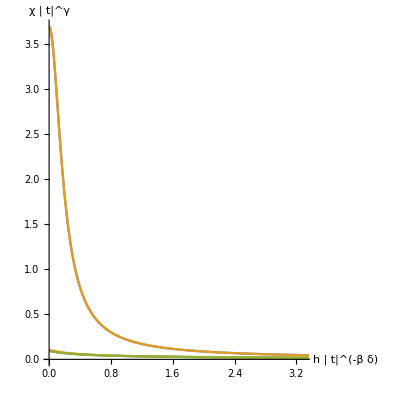

```mathematica
pSus=Show[ParametricPlot[Evaluate@{
{uh[Data[2]["θ0"],Data[2]["gs"]][1,γ Data[2]["θ0"]] Abs[ut[1,γ Data[2]["θ0"]]]^(-15/8),-(DufDuh@@PrepareArgument[Data[2]])[2][1,γ Data[2]["θ0"]] Abs[ut[1,γ Data[2]["θ0"]]]^(7/4)},
{uh[Data[6]["θ0"],Data[6]["gs"]][1,γ Data[6]["θ0"]] Abs[ut[1,γ Data[6]["θ0"]]]^(-15/8),-(DufDuh@@PrepareArgument[Data[6]])[2][1,γ Data[6]["θ0"]] Abs[ut[1,γ Data[6]["θ0"]]]^(7/4)}
},{γ,0,0.999},PlotRange->{{0,3.3},Automatic},
AspectRatio->1,WorkingPrecision->20,PlotPoints->50,AxesLabel->{"h | t|^(-β δ)","χ | t|^γ"},LabelStyle->{Black,FontSize->14}
],pCasS]
```

```mathematica
Export["/tmp/pMag.pdf",pMag];
Export["/tmp/pSus.pdf",pSus]
```

/tmp/pSus.pdf

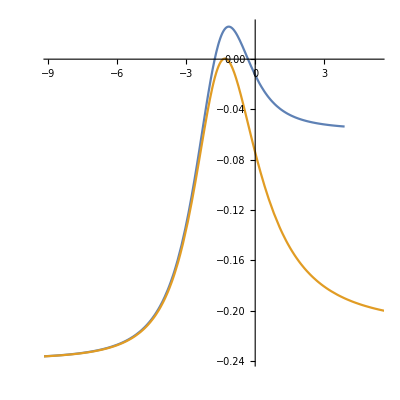

```mathematica
p2=ParametricPlot[Evaluate@{
{ut[1,γ Data[2]["θ0"]](uh[Data[2]["θ0"],Data[2]["gs"]][1,γ Data[2]["θ0"]])^(-8/15),-(DufDut@@PrepareArgument[Data[2]])[2][1,γ Data[2]["θ0"]]},
{ut[1,γ Data[6]["θ0"]](uh[Data[6]["θ0"],Data[6]["gs"]][1,γ Data[6]["θ0"]])^(-8/15),-(DufDut@@PrepareArgument[Data[6]])[2][1,γ Data[6]["θ0"]]}
},{γ,0,0.99},
AspectRatio->1
]
```

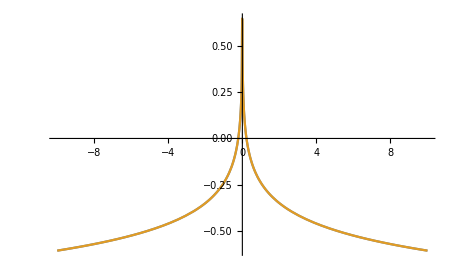

```mathematica
p2=Plot[{
-Re[Evaluate[DufDut@@PrepareArgument[Data[2]]][2]@@InverseCoordinates[Data[2]["θ0"],Data[2]["gs"]][t,1/10000]],
-Re[Evaluate[DufDut@@PrepareArgument[Data[6]]][2]@@InverseCoordinates[Data[6]["θ0"],Data[6]["gs"]][t,1/10000]]
},{t,-10,10},PlotRange->All,Exclusions->None]
```

```mathematica
InverseCoordinates[Data[6]["θ0"],Data[6]["gs"]][-1,0]
```

{1.00000000000000006670304521022465239,0}

```mathematica
dat=Table[{uhh,Re[Evaluate[DufDuh@@PrepareArgument[Data[6]]][2]@@InverseCoordinates[Data[6]["θ0"],Data[6]["gs"]][-1/100,uhh]]},{uhh,-1,1,0.005}];
```

```mathematica
InverseCoordinates-1/10,0]
```

InverseCoordinates[1/10,0]

```mathematica
dat[[1]]
```

{-10.,-0.000959513527053}

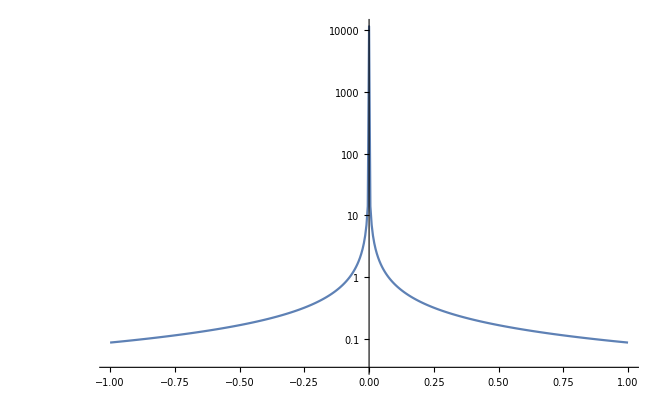

```mathematica
ListLogPlot[-dat,Joined->True,PlotRange->All]
```

```mathematica
p6=Plot[Re[Evaluate[DufDuh@@PrepareArgument[Data[6]]][2]@@InverseCoordinates[Data[6]["θ0"],Data[6]["gs"]][ut,1/100]],{ut,-10,10},PlotRange->All,Exclusions->None]
```

-Graphics-

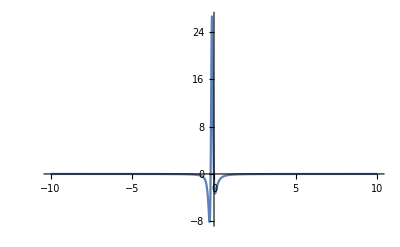

```mathematica
p6=Plot[Re[Evaluate[DufDut@@PrepareArgument[Data[6]]][4]@@InverseCoordinates[Data[6]["θ0"],Data[6]["gs"]][ut,1/100]],{ut,-10,10},PlotRange->All,Exclusions->None]
```

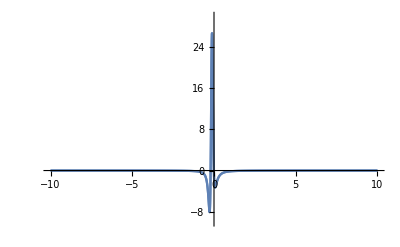

```mathematica
Show[p2,p6,PlotRange->{-10,30}]
```

```mathematica
Solve[{tt==R(θ^2-1),h==R^Δ g[θ]},{R,θ}]
```

$Aborted

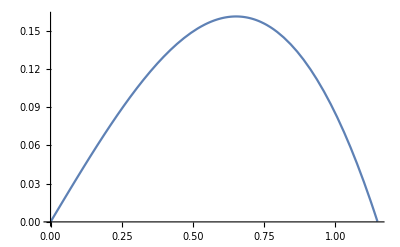

```mathematica
Plot[Evaluate[g[θ0,{g[0],g[1]}][θ]/.data2],{θ,0,1.148}]
```

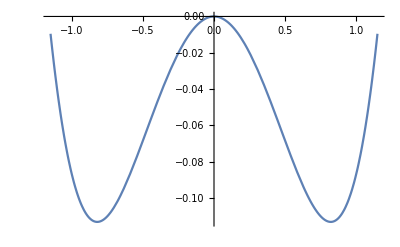

```mathematica
Plot[(uf@@Most[prep2])[1,θ],{θ,-1.148,1.148}]
```

```mathematica
dat=Flatten[Table[{ut[R,θ],uh[θ0,{g[0],g[1]}][R,θ],-(DufDuh@@prep2)[1][R,θ]}/.data2,{R,0.05,2,0.05},{θ,-1.14841,1.14841,0.05}],1];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
ListPlot3D[dat]
```

-Graphics3D-

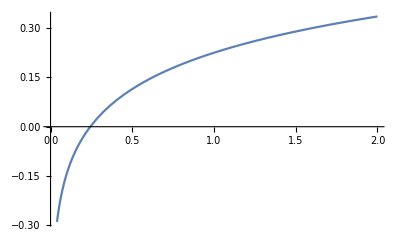

```mathematica
Plot[Evaluate[(DufDut@@prep2)[2][R,0.1]],{R,0,2}]
```

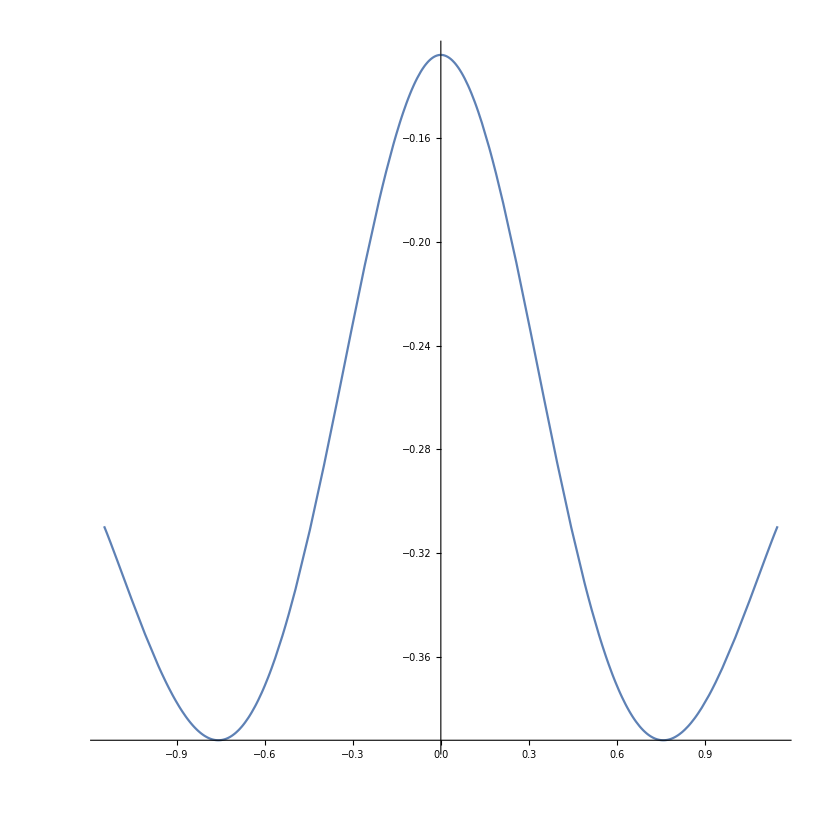

```mathematica
ParametricPlot[{θ,Evaluate[(DufDut@@prep2)[2][.1,θ]]},{θ,-1.148,1.148},AspectRatio->1]
```

```mathematica
dGdξ
```

```mathematica
(dΦdηList@@prep2)[0,1]
```

{-1.19741+0. ⅈ}

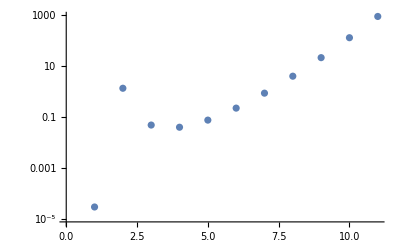

```mathematica
ListLogPlot[Abs[(DScriptFPlusMinusDξθ0List@@prep2)[10]]]
```

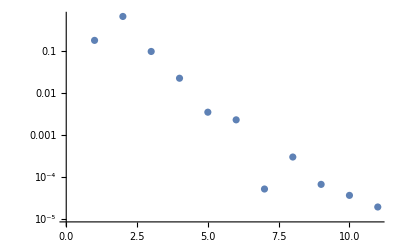

```mathematica
ListLogPlot[Abs[(DScriptF0DηList@@prep2)[10,0.5]]]
```